```mathematica
n= 10000;
K= 5000;
X= TransformedDistribution[2x-1,x\[Distributed]BernoulliDistribution[1/2]];
```

```mathematica
f[x_,y_] := x+ If[y>=0,1,0]
```

```mathematica
t = Table[
u=Accumulate[RandomVariate[X,n]];
Fold[f,0,u]/n
,K];
```

```mathematica
bins = Table[x,{x,0,1,0.05}]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

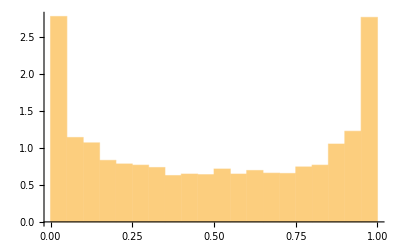

```mathematica
Histogram[t,{bins}, "PDF"]
```